# KerrNullGeodesics

The KerrNullGeodesics` package contains functions for calculating the null geodesic motion in the Kerr metric. The public functions in this package are:

KerrNullGeopaclet:BlackHoleImagesKerrNullGeodesics/ref/KerrNullGeo[a,xs,ps] | returns a KerrNullGeoFunction which stores information about the trajectory of a light-ray starting from specified initial conditions. The black hole spin a, position xs, and wavevector ps are assumed to be given in units of the BH mass, unless mass M is specified (optional argument).
KerrNullGeoDistantpaclet:BlackHoleImages/ref/KerrNullGeoDistant[a,θo,α,β,shellRadius_:50, radiusLimit_:0] | returns a KerrNullGeoDistantFunction which stores information about the trajectory of a geodesic coming from infinity. The spin a, and Bardeen's impact parameters α, β are assumed to be given in units of the BH mass
KerrNullGeoFunction[a,xs,ps,M,assoc] | an object for storing the trajectory and its parameters in the assoc association
KerrNullGeoDistantFunction[a,θo,α,β,assoc] | an object for storing the trajectory and its parameters in the assoc association

First, load the paclet:

```mathematica
Needs["BlackHoleImages`"]
```

## The Conventions in This Package

Throughout the paclet, we assume the Kerr geometry characterized by the black hole's mass M and its spin parameter a. In this package, the unit convention c=G=M=1 is used, so that all the calculations are dimensionless.

We use the standard Boyer-Lindquist coordinates (t,r, θ, ϕ), and parametrize the geodesics with the Mino time λ defined by (d x^μ)/(d λ)= (r^2+a^2 Cos[θ])/E p^μ.

The constants of motion are in the referred to as ℓ=L/E, the angular momentum over energy at infinity, and η=Q/E^2, where Q is the Carter integral.

## The Distant Observer Case

For generating the null geodesics in the case of an observer far away from the black hole, the KerrNullGeoDistantpaclet:BlackHoleImages/ref/KerrNullGeoDistant function is implemented.

First of all, it is necessary to use a characterization of the angular displacement projected on the observer’s celestial sphere, which would not be proportional to the distance r. This is often done using so-called Bardeen coordinates (found in Bardeen’s lecture in Houches Ecole d’ete de Physique Theorique, isbn 978-0-677-15610-1), defined as   α=-r_o p^[ϕ]/p^[t],  β=-r_o p^[θ]/p^[t],  where the indices in square brackets denote the four-momentum measured by local observer, whose  r=r_o and θ=θ_o coordinates are fixed and who possesses zero angular momentum. The Bardeen coordinates can be used to calculate the integrals of motion and their straight-forward interpretation is useful for plotting images in the case r_o→∞.

The time coordinate t cannot be readily obtained from the relations found in Gralla & Lupsasca, arXiv:1910.12881v3 in the distant observer case, however one can obtain sensible relation for  Δv=v_f−v_i , where we define the null time v = t + r + 2 Log[r/2]. We here assume the geodesic begins at the spatial infinity and moves in time towards the coordinate centre.

A single geodesic can be generated with the  KerrNullGeoDistantpaclet:BlackHoleImages/ref/KerrNullGeoDistant function by specifying:

a | The spin parameter.
θo | The  distant observer's θ coordinate.
α, β | The bardeen coordinates of the geodesic.
shellRadius | Optional parameter which specifies the radius (given in multiples of the black hole's mass) at which a stellar background is considered to be in the StellarBackgroundFromTemplate function.
radiusLimit | Optional parameter which specifies the maximal radius (given in multiples of the black hole's mass) at which an accration disk is considered.

Additional options can be given:

Option | Default | Description
"Rotation" | "Counterclockwise" | Sets the direction of rotation of the black hole. The default option is 
"Rotation"-> "Counterclockwise".  The opposite is
"Rotation"-> "Clockwise".
"PhiRange" | {-Infinity, Infinity} | Sets the range of output of the azimuthal angle. The default is "PhiRange"-> {−∞, ∞}, which starts the coordinate at 0 and does not take the modulus of it after full windings. Typical options could be {−π, π}
or {0, 2π}, but other option values in the format {bottomvalue, topvalue} are valid as well.

The  KerrNullGeoDistantpaclet:BlackHoleImages/ref/KerrNullGeoDistant function returns a KerrNullGeoDistantFunction object which stores information about the trajectory of a geodesic coming from infinity in an association accepting the following keys:

"Trajectory" | Returns a list of trajectory coordinates {Δv, r, θ, φ} as functions of the Mino time λ.
"ConstantsOfMotion" | Returns a list of the constants of motion of the geodesic {ℓ, η}.
"RadialRoots" | Returns the radial roots  in a list {r1, r2, r3, r4}, as are defined in Gralla & Lupsasca, arXiv:1910.12881v3.
"EquatorIntersectionMinoTimes" | Returns the Mino times when  θ=π/2 in a list from smallest (closest to the observer) to largest.
"EquatorIntersectionCoordinates" | Returns the coordinates {Δv,  r,  φ} at "EquatorIntersectionMinoTimes".
"ShellIntersectionMinoTime" | Returns the Mino time when the geodesic of the type "PhotonEscape" crosses the radius given by shellRadius at the higher Mino time (further from the observer). 
"ShellIntersectionCoordinates" | Returns the coordinates {θ, ϕ, Δv} at  "ShellIntersectionMinoTime".
"TrajectoryType" | Returns one of the following trajectory types: "PhotonCapture" if the trajectory crosses the horizon, or else "PhotonEscape".
"MinoTimeOfCapture" | Returns the Mino time,when the photon crosses the outer horizon if "TrajectoryType" is "PhotonCapture", or the Mino time when the photon scatters back to infinity.
"EscapeCoordinates" | If "TrajectoryType" is "PhotonEscape", returns the {θ, φ} coordinates in "MinoTimeOfCapture", otherwise returns {-1, -1}.
"EmissionCoordinates" | If the trajectory crosses the equatorial plane at some
r>rISCO, returns a list of coordinates at the first occurrence.
"EmissionParameters | If the trajectory crosses the equatorial plane at some
r>rISCO, at the first occurrence returns a list {κ, θloc, φloc} defined as the ratio between energy at infinity and the locally measured energy on a circular equatorial geodesic, and the locally measured impact angles respectively. Otherwise returnes {-1, -1, -1}.

As an example, let us generate a geodesic in a geometry defined by the spin parameter a = 0.4 coming from θo = π/3 and possessing the Bardeen coordinate α=5, β=5:

```mathematica
geod = KerrNullGeoDistant[0.4, π/3, 5, 5];
```

Let us see if the geodesic crosses the horizon or stays outside of it:

```mathematica
If[geod["TrajectoryType"]=="PhotonCapture", Print["Crosses the horizon."], Print["Stays outside of the horizon."]]
```

Stays outside of the horizon.

From e.g. Gralla & Lupsasca, arXiv:1910.12881v3, we know that the geodesics scattering on the black hole should have all the roots of the radial potential real. Let us check if that is the case:

```mathematica
geod["RadialRoots"]
```

{-7.9589+0. ⅈ,0.047651+0. ⅈ,2.38086+0. ⅈ,5.53039+0. ⅈ}

Let us also look at the constants of motion:

```mathematica
Print["ℓ = ",geod["ConstantsOfMotion"][[1]]]
Print["η = ", geod["ConstantsOfMotion"][[2]]]
```

ℓ = -(5 √3)/2

η = 31.21

To visualize the geodesics, we might want to know what the Mino time of the geodesic's escape to infinity λ_∞ is:

```mathematica
Subscript[λ, ∞] = geod["MinoTimeOfCapture"]
```

0.627646

To access the coordinate as functions of the Mino time, one does not need to specify the "Trajectory" key, the value of Mino time suffices.

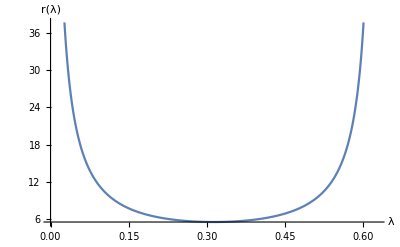

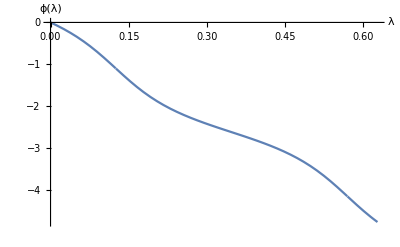

```mathematica
Plot[geod[λ][[2]], {λ, 0, Subscript[λ, ∞]},AxesLabel->{λ,r[λ]}]
Plot[geod[λ][[4]], {λ, 0, Subscript[λ, ∞]},AxesLabel->{λ,ϕ[λ]}]
```

Note that since we did not specify the option "PhiRange" of KerrNullGeoDistantpaclet:BlackHoleImages/ref/KerrNullGeoDistant, the ϕ as  a funtion of λ is not a priori bounded.

Let us plot the geodesic's space-like coordinates as spherical coordinates in the Euclidian space:

```mathematica
Spherical2Cartesian[list_]:={list[[2]] Sin[list[[3]]] Cos[list[[4]]], list[[2]] Sin[list[[3]]] Sin[list[[4]]], list[[2]] Cos[list[[3]]]};
plotA = ParametricPlot3D[Spherical2Cartesian[geod[λ]],{λ,0,Subscript[λ, ∞]},PlotPoints->1000, PlotRange->{{-15,15},{-15,15},{-15,15}}];
plotB= SphericalPlot3D[1+√(1-0.4^2),{θ,-π,π},{ϕ,0,2 π}, PlotStyle->Directive[Black], PlotRange->{{-15,15},{-15,15},{-15,15}}, AxesLabel->{"x", "y", "z"}];
Show[{plotA, plotB}, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

As a final example, let us compute the angle δ between the incoming direction of the geodesic and the direction after scattering:

```mathematica
{Subscript[θ, e],Subscript[ϕ, e]} = geod["EscapeCoordinates"];
θo = π/3;
δ = ArcCos[-Sin[Subscript[θ, e]]Sin[π-θo] Cos[Subscript[ϕ, e]] + Cos[Subscript[θ, e]] Cos[π-θo]];
Print["δ = ", δ, " rad"]
```

δ = 1.23853 rad

## The Observer at Finite Distance

If the initial data are given at a point at finite distance from the black hole, one can use the KerrNullGeopaclet:BlackHoleImagesKerrNullGeodesics/ref/KerrNullGeo function.

The geodesic in this case is generating by specifying the following values:

a | The spin parameter.
xs | Initial position 4-vector.
ps | Initial momentum.

This can be further modified with the following options:

Option | Default | Description
"Momentum" | "Momentum" | Specifies whether the user provided 
4-momentum or wave 
4-vector as ps. The default option 
is "Momentum"->"Momentum". If the
user provided the wave 4-vector,the option 
"Momentum"->"WaveVector" should
be specified.
"PhiRange" | {-Infinity, Infinity} | Sets the range of output of the azimuthal angle. The default is "PhiRange"-> {−∞, ∞}, which starts the coordinate at 0 and does not take the modulus of it after full windings. Typical options could be {−π, π}
or {0, 2π}, but other option values in the format {bottomvalue, topvalue} are valid as well.

Similarly  to KerrNullGeoDistantpaclet:BlackHoleImages/ref/KerrNullGeoDistant, the KerrNullGeopaclet:BlackHoleImagesKerrNullGeodesics/ref/KerrNullGeo function returns a KerrNullGeoFunction object which stores information about the trajectory of a geodesic in an association accepting the following keys:

"Trajectory" | Returns a list of trajectory coordinates {t, r, θ, φ} as functions of the Mino time λ.
"ConstantsOfMotion" | Returns a list of the constants of motion of the geodesic {ℓ, η}.
"RadialRoots" | Returns the radial roots  in a list {r1, r2, r3, r4}, as are defined in Gralla & Lupsasca, arXiv:1910.12881v3.
"EquatorIntersectionMinoTimes" | Returns the Mino times when  θ=π/2 in a list from smallest (closest to the observer) to largest.
"EquatorIntersectionCoordinates" | Returns the coordinates {t,  r,  φ} in "EquatorIntersectionMinoTimes".
"TrajectoryType" | Returns one of the following trajectory types: "PhotonCapture" if the trajectory crosses the horizon, or else "PhotonEscape".
"MinoTimeOfCapture" | Returns the Mino time,when the photon crosses the outer horizon if "TrajectoryType" is "PhotonCapture", or the Mino time when the photon scatters back to infinity.
"EscapeCoordinates" | If "TrajectoryType" is "PhotonEscape", returns the {θ, φ} coordinates in "MinoTimeOfCapture", otherwise returns {-1, -1}.
"EmissionCoordinates" | If the trajectory crosses the equatorial plane at some
r>rISCO, returns a list of coordinates at the first occurrence.
"EmissionParameters | If the trajectory crosses the equatorial plane at some
r>rISCO, at the first occurrence returns a list {κ, θloc, φloc} defined as the ratio between energy at infinity and the locally measured energy on a circular equatorial geodesic, and the locally measured impact angles respectively. Otherwise returnes {-1, -1, -1}.

Let us now generate a geodesic in a geometry characterized by the spin parameter a = 0.9,  starting from the position  xs={0,1.436,π/3,0} with the 4-momentum  ps={-1,1,√(10,10}). The 4-momentum in fact is not normalized to 0, which would be required from a null vector, but since only the sign of the radial component of the 4-momentum is used in the code, it plays no role.

```mathematica
geod1 = KerrNullGeo[0.9, {0, 1.436, π/3, 0}, {-1, 1, Sqrt[10], 10}];
```

Let us see if the geodesic crosses the horizon or stays outside of it:

```mathematica
If[geod1["TrajectoryType"]=="PhotonCapture", Print["Crosses the horizon."], Print["Stays outside of the horizon."]]
```

Crosses the horizon.

We can check that all the roots of the radial potential are real and  the initial radial coordinate is smaller then r_3 meaning that the geodesics never escapes to the spatial infinity but falls back on the horizon.

```mathematica
ro = 1.436;
{r1, r2, r3, r4} = geod1["RadialRoots"]
If[ro<r3, Print["ro<r3"], Print["ro>r3"]]
```

{-12.74+0. ⅈ,0.151701+0. ⅈ,1.65306+0. ⅈ,10.9352+0. ⅈ}

ro<r3

Let us get the Mino time of the photon falling on the outer horizon and plot the radial and polar coordinates as functions of λ:

0.134814

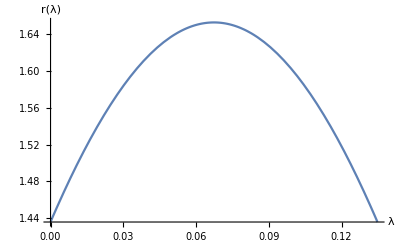

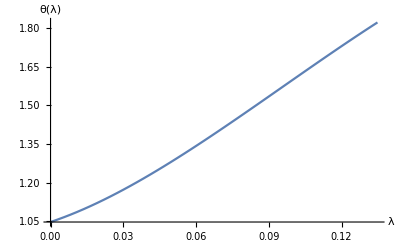

```mathematica
Subscript[λ, x] = geod1["MinoTimeOfCapture"]
Plot[geod1[λ][[2]], {λ, 0, Subscript[λ, x]},AxesLabel->{λ,r[λ]}]
Plot[geod1[λ][[3]], {λ, 0, Subscript[λ, x]},AxesLabel->{λ,θ[λ]}]
```

Let us plot the geodesic's space-like coordinates as spherical coordinates in the Euclidian space:

```mathematica
plot1A = ParametricPlot3D[Spherical2Cartesian[geod1[λ]],{λ,0,Subscript[λ, x]},PlotPoints->1000, PlotRange->{{-2,2},{-2,2},{-2,2}}];
plot1B= SphericalPlot3D[1+√(1-0.9^2),{θ,-π,π},{ϕ,0,2 π}, PlotStyle->Directive[Black], PlotRange->{{-2,2},{-2,2},{-2,2}}, AxesLabel->{"x", "y", "z"}];
Show[{plot1A, plot1B}, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

.

We see that the geodesic crosses the equatorial plane one time. Let us see the Mino time and coordinates of that intersection:

```mathematica
Subscript[λ, eq] = geod1["EquatorIntersectionMinoTimes"][[1]];
{Subscript[t, eq], Subscript[r, eq], Subscript[ϕ, eq]} = geod1["EquatorIntersectionCoordinates"];
Print["λ_eq = ",Subscript[λ, eq]]
Print["t_eq = ", Subscript[t, eq][[1]]]
Print["r_eq = ", Subscript[r, eq][[1]]]
Print["ϕ_eq = ", Subscript[ϕ, eq][[1]]]
```

λ_eq = 0.0955312

t_eq = -29.9771

r_eq = 1.6137

ϕ_eq = -8.15944

Related Guides

KerrNullGeodesics

Related Tech Notes

KerrImages

AlphaDiskModel

## Metadata

### Categorization

Tech Note

BlackHoleImages

BlackHoleImages`

BlackHoleImages/tutorial/KerrNullGeodesics

### Keywords